```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Parameters=Import["../Parameters"]

fsTitle=24;
fsAxesLabel=18;
fs2=16;

n=Parameters[[3,2]];

IntactPF=Import["../Intact/PartitionFunction_0_0.out","Table"];
IntactFE=Import["../Intact/FreeEnergy_0_0.out","Table"];
IntactdFE=Import["../Intact/dFreeEnergy_0_0.out","Table"];

FrayedData=Table[{
Import["PartitionFunction_0_"<>ToString[i]<>".out","Table"],
Import["FreeEnergy_0_"<>ToString[i]<>".out","Table"],
Import["dFreeEnergy_0_"<>ToString[i]<>".out","Table"]
}
,{i,1,(n-1)}
];
```

{{L:,40.2},{m:,100},{N:,12},{kappa:,0.1},{sigma:,0.0012},{kappa_sigma_r:,83.3333},{Delta:,0.2},{Extension Minimum:,0},{Extension Maximum:,70},{e0:,0.04},{Beta:,38.6817},{etab_b:,2.3}}

## Numerical Results - Frayed

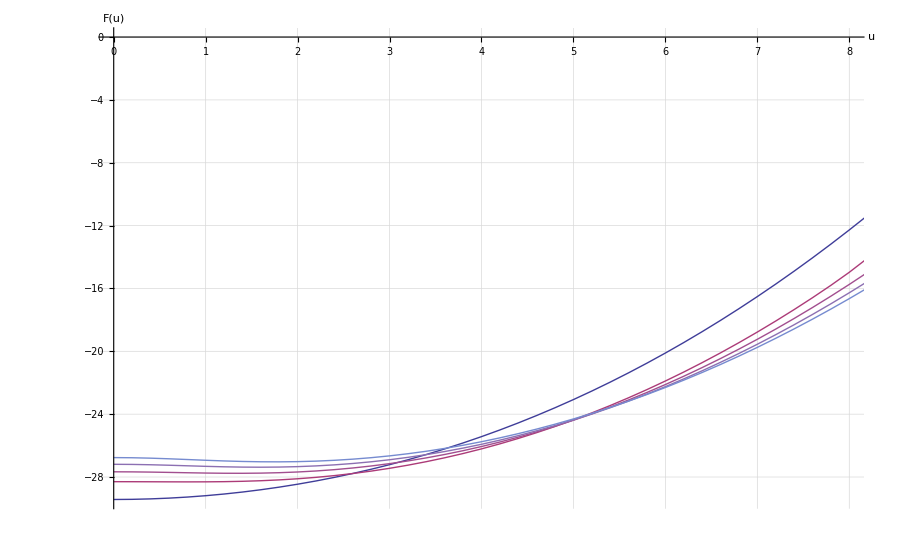

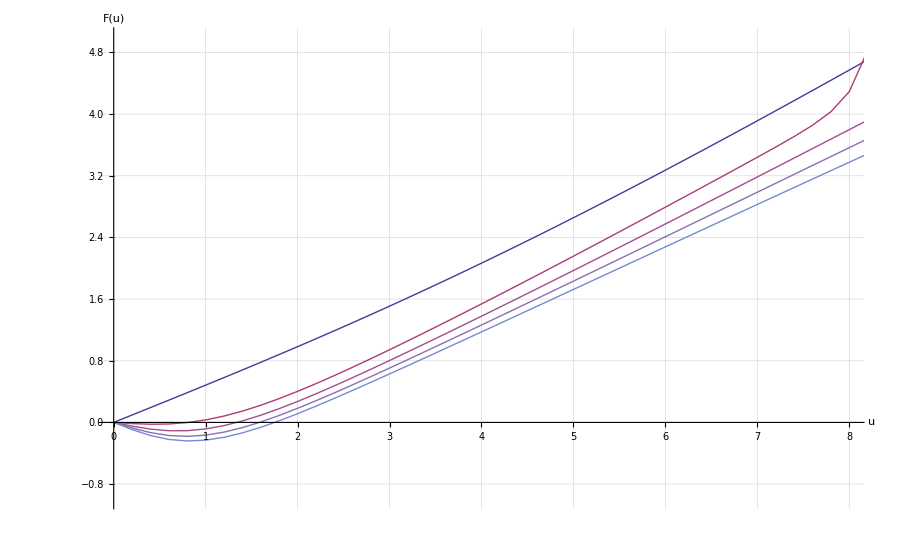

```mathematica
f1=1;
f2=2;
f3=3;
f4=4;

FrayedFE=ListLinePlot[
{
IntactFE,
FrayedData[[f1,2]],
FrayedData[[f2,2]],
FrayedData[[f3,2]],
FrayedData[[f4,2]]
},
PlotRange->{{0,8}},
ImageSize->{900,600},
PlotStyle->{{Thick},{Thick,ColorData["Atoms"]["Lr"]},{Thick,ColorData["Atoms"]["Fm"]},{Thick,ColorData["Atoms"]["Cm"]},{Thick,ColorData["Atoms"]["Np"]}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},
LabelStyle->{"Times",FontSize->fs2},
PlotLegend->{
Style["Intact",FontSize->fs2],
Style["Frayed "<> ToString[f1],FontSize->fs2],
Style["Frayed "<> ToString[f2],FontSize->fs2],
Style["Frayed "<> ToString[f3],FontSize->fs2],
Style["Frayed "<> ToString[f4],FontSize->fs2]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.4,0.4},
LegendPosition->{-0.8,0.05}
]

FrayeddFE=ListLinePlot[
{
IntactdFE,
FrayedData[[f1,3]],
FrayedData[[f2,3]],
FrayedData[[f3,3]],
FrayedData[[f4,3]]
},
PlotRange->{{0,8},{-1,5}},
ImageSize->{900,600},
PlotStyle->{{Thick},{Thick,ColorData["Atoms"]["Lr"]},{Thick,ColorData["Atoms"]["Fm"]},{Thick,ColorData["Atoms"]["Cm"]},{Thick,ColorData["Atoms"]["Np"]}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},
LabelStyle->{"Times",FontSize->fs2},
PlotLegend->{
Style["Intact",FontSize->fs2],
Style["Frayed "<> ToString[f1],FontSize->fs2],
Style["Frayed "<> ToString[f2],FontSize->fs2],
Style["Frayed "<> ToString[f3],FontSize->fs2],
Style["Frayed "<> ToString[f4],FontSize->fs2]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.4,0.4},
LegendPosition->{-0.8,0.05}
]
```